```mathematica
(* Available Plays:
1. Antigone
2. Death of a Salesman
3-22. Hamlet
23-48. King Lear
49-57. Midsummer Night's Dream
58. Oedipus At Colonus
59. Oedipus The King
60-83. Romeo and Juliet
84. The Glass Menagerie
85-93 The Tempest *)
(* play#, negativitybias, positive tolerance, negative tolerance, startInd, endInd *)
plays={"Antigone", "Death of a Salesman", "Hamlet", "King Lear", "Midsummer Night's Dream", "Oedipus At Colonus", "Oedipus The King", "Romeo and Juliet", "The Tempest", "The Glass Menagerie"};
playConditions=Table[plays⟦i⟧->{i,1,.30,-.30},{i,1,Length[plays]}];
exceptions={
Values[playConditions⟦1⟧]->{1,1.2,.20,-.30},
Values[playConditions⟦2⟧]->{2,1.35,.3,-.2},
Values[playConditions⟦3⟧]->{3,1.25,.40,-.30},
Values[playConditions⟦4⟧]->{4,1.3,.30,-.30},
Values[playConditions⟦5⟧]->{5,1.3,.30,-.30},
Values[playConditions⟦6⟧]->{6,1.3,.30,-.30},
Values[playConditions⟦7⟧]->{7,1.3,.30,-.30},
Values[playConditions⟦8⟧]->{8,1.3,.30,-.30},
Values[playConditions⟦9⟧]->{9,1.3,.30,-.30},
Values[playConditions⟦10⟧]->{10,1.2,.30,-.30}};
playConditions=playConditions/.exceptions;
playNum=10;
```

```mathematica
(* Process Plays *)
SetDirectory[NotebookDirectory[]];
files=FileNames["*.txt",NotebookDirectory[]];
text=StringJoin[Import[#]&/@files⟦85;;93⟧];
speakerOrder=Capitalize[ToLowerCase@StringCases[text,Shortest["<b>"~~x__~~"</b>"]->x]//Flatten,"AllWords"];
nameList=speakerOrder//DeleteDuplicates;
```

```mathematica
(* Separates lines of text ready for sentiment analysis *)
lines=StringSplit[text//StringDelete[Shortest["<i>"~~x__~~"</i>"]]//StringDelete[Shortest["["~~x__~~"]"]],Shortest["<b>"~~x__~~"</b>"]]//StringDelete[Shortest["<"~~x___~~">"]]//Rest;
sentences=lines//TextSentences;
lineLength=Length/@sentences;
```

```mathematica
(* Create directed edges for graph *)
speakerBySentence=Table[Table[speakerOrder⟦i⟧,Length[sentences⟦i⟧]],{i,1,Length[lines]}]//Flatten;
recipientByLine=Prepend[Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}],Table[speakerOrder⟦2⟧,Length[First[sentences]]]];
recipientBySentence=Nest[Prepend[speakerOrder⟦2⟧],Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}]//Flatten,Length[First[sentences]]];

emphasis=WordFrequency[Flatten[sentences],#,IgnoreCase->True]&/@nameList;
diffRecipientPos=SortBy[Position[emphasis,_?Positive],Last];

brokenInd=TakeList[Range[Length[recipientBySentence]],lineLength];
sentenceToLineRules=Table[i->First@@Position[brokenInd,i],{i,1,Length[recipientBySentence]}];
lineIndOfSentences=Range[Length[recipientBySentence]]/.sentenceToLineRules;
sentenceNumOfDiffLine[x_]:=Last@diffRecipientPos⟦x⟧-Total[lineLength⟦;;lineIndOfSentences⟦Last@diffRecipientPos⟦x⟧⟧-1⟧];

For[i=1,i≤Length[diffRecipientPos],i++,
recipientByLine⟦lineIndOfSentences⟦Last@diffRecipientPos⟦i⟧⟧,sentenceNumOfDiffLine[i];;⟧=nameList⟦First@diffRecipientPos⟦i⟧⟧]

recipientBySentence=recipientByLine//Flatten;
finalRules=Table[speakerBySentence⟦i⟧->recipientBySentence⟦i⟧,{i,1,Length[speakerBySentence]}];
ruleList=DeleteCases[DeleteDuplicates[finalRules],x_->x_];
```

```mathematica
(* Implement Sentiment Analysis of lines *)
feelings=Classify["Sentiment",#,"Probabilities"]&/@sentences//Flatten;
```

```mathematica
(* Put sentiment into edges *)
{pos,neu,neg}=Table[feelings⟦i⟧[#],{i,1,Length[feelings]}]&/@{"Positive","Neutral","Negative"};
negBias=Values[playConditions]⟦playNum⟧⟦2⟧;
Health=(pos-negBias*neg)/(1+neu);
sentenceHealth={finalRules⟦#⟧,Health⟦#⟧}&/@Range[Length[Health]];
sentenceHealthFormat=Cases[sentenceHealth,{#,_}]&/@ruleList;
relationshipHealth=Table[Mean[Table[sentenceHealthFormat⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sentenceHealthFormat⟦i⟧]}]],{i,1,Length[sentenceHealthFormat]}];
```

```mathematica
(* Incorporate Frequency for into Health *)
freq=Table[Length[sentenceHealthFormat⟦i⟧],{i,1,Length[sentenceHealthFormat]}];
freqMultiplier[x_]:=(Log[x]+2)/2;
thickness=N[freq]/Max[N[freq]]*.012;
edgeWidth=Table[ruleList⟦i⟧->freqMultiplier[N[freq⟦i⟧]],{i,Length[ruleList]}];
```

```mathematica
(* Exclude Neutral/Conflicted Relationships *)
relationshipHealthFinal=relationshipHealth*N[freqMultiplier[freq]];
posTolerance=Values[playConditions]⟦playNum⟧⟦3⟧;
negTolerance=Values[playConditions]⟦playNum⟧⟦4⟧;

viableEdges=Position[relationshipHealthFinal,x_/;x>posTolerance||x<negTolerance]//Flatten;
relationshipHealthFinalExc=Table[relationshipHealthFinal⟦i⟧,{i,viableEdges}];
viableFreq=Table[freq⟦i⟧,{i,viableEdges}];
viableThickness=Table[thickness⟦i⟧,{i,viableEdges}];
viableEdgeWidth=Table[edgeWidth⟦i⟧,{i,viableEdges}];
```

```mathematica
(* Modify the Graph with color (health) and width (frequency) *)
relationshipColors=Table[Blend[{Red,Gray,Green},(i+1)/2],{i,relationshipHealthFinalExc}]
```

{RGBColor[0.18000157068348388, 0.8199984293165161, 0.18000157068348388],RGBColor[0.14962244207192166, 0.8503775579280783, 0.14962244207192166],RGBColor[0.3055179515150823, 0.6944820484849177, 0.3055179515150823],RGBColor[0.7850434860125982, 0.2149565139874018, 0.2149565139874018],RGBColor[0.2807753338925827, 0.7192246661074173, 0.2807753338925827],RGBColor[0.7736153578709641, 0.2263846421290358, 0.2263846421290358],RGBColor[0.3361741136098243, 0.6638258863901757, 0.3361741136098243],RGBColor[0.2852506853263228, 0.7147493146736772, 0.2852506853263228],RGBColor[0.10378533873165141, 0.8962146612683486, 0.10378533873165141],RGBColor[0., 1., 0.],RGBColor[0.2420267315975766, 0.7579732684024234, 0.2420267315975766],RGBColor[0.3263655892234848, 0.6736344107765152, 0.3263655892234848],RGBColor[0.3019341500194994, 0.6980658499805006, 0.3019341500194994],RGBColor[0.2661158464611071, 0.7338841535388929, 0.2661158464611071],RGBColor[0.2749943542799371, 0.7250056457200629, 0.2749943542799371],RGBColor[0.2523246609642602, 0.7476753390357398, 0.2523246609642602],RGBColor[0.3127008448957459, 0.6872991551042541, 0.3127008448957459],RGBColor[0.744045694756366, 0.25595430524363405, 0.25595430524363405],RGBColor[0.24407665493382802, 0.755923345066172, 0.24407665493382802],RGBColor[0.06885450679429383, 0.9311454932057062, 0.06885450679429383],RGBColor[0.2810758379804673, 0.7189241620195327, 0.2810758379804673],RGBColor[0.28995624847402823, 0.7100437515259718, 0.28995624847402823],RGBColor[0.046243106703116266, 0.9537568932968837, 0.046243106703116266],RGBColor[0.2047316313562494, 0.7952683686437506, 0.2047316313562494],RGBColor[0.328009580085851, 0.671990419914149, 0.328009580085851],RGBColor[0.20367799355685035, 0.7963220064431497, 0.20367799355685035],RGBColor[0.7861360383394485, 0.21386396166055155, 0.21386396166055155],RGBColor[0.1771291262658108, 0.8228708737341892, 0.1771291262658108],RGBColor[0.29943716958873645, 0.7005628304112635, 0.29943716958873645],RGBColor[0.3291440982898215, 0.6708559017101785, 0.3291440982898215],RGBColor[0.3482929641312913, 0.6517070358687087, 0.3482929641312913],RGBColor[0.3239138864564681, 0.6760861135435319, 0.3239138864564681],RGBColor[0.03333801877571252, 0.9666619812242875, 0.03333801877571252],RGBColor[0.2652059854801365, 0.7347940145198635, 0.2652059854801365],RGBColor[0.25270146804738314, 0.7472985319526169, 0.25270146804738314],RGBColor[0.10227446958339037, 0.8977255304166096, 0.10227446958339037],RGBColor[0.813162946991753, 0.186837053008247, 0.186837053008247],RGBColor[0.6958071228881917, 0.3041928771118083, 0.3041928771118083],RGBColor[0.28997443348624263, 0.7100255665137574, 0.28997443348624263],RGBColor[0.6631783235118248, 0.3368216764881752, 0.3368216764881752],RGBColor[0.18414555245541397, 0.815854447544586, 0.18414555245541397],RGBColor[0.3341379888138083, 0.6658620111861917, 0.3341379888138083],RGBColor[0.6675267424605313, 0.33247325753946866, 0.33247325753946866],RGBColor[0.2250855790871289, 0.7749144209128711, 0.2250855790871289],RGBColor[0.14985511323003198, 0.850144886769968, 0.14985511323003198],RGBColor[0.18064336127660718, 0.8193566387233928, 0.18064336127660718],RGBColor[0., 1., 0.],RGBColor[0.2176176236054509, 0.7823823763945491, 0.2176176236054509],RGBColor[0.6849972576632526, 0.3150027423367474, 0.3150027423367474],RGBColor[0., 1., 0.],RGBColor[0.7371472741128136, 0.26285272588718644, 0.26285272588718644],RGBColor[0.26482679886604843, 0.7351732011339516, 0.26482679886604843],RGBColor[0.015171172604161232, 0.9848288273958388, 0.015171172604161232],RGBColor[0.7043441966932971, 0.2956558033067029, 0.2956558033067029],RGBColor[1., 0., 0.],RGBColor[0.17335206892193533, 0.8266479310780647, 0.17335206892193533],RGBColor[0.26358181081016374, 0.7364181891898363, 0.26358181081016374]}

```mathematica
viableRules=Table[ruleList⟦i⟧,{i,viableEdges}];
edgeColors=Table[viableRules⟦i⟧->relationshipColors⟦i⟧,{i,Length[viableRules]}];
```

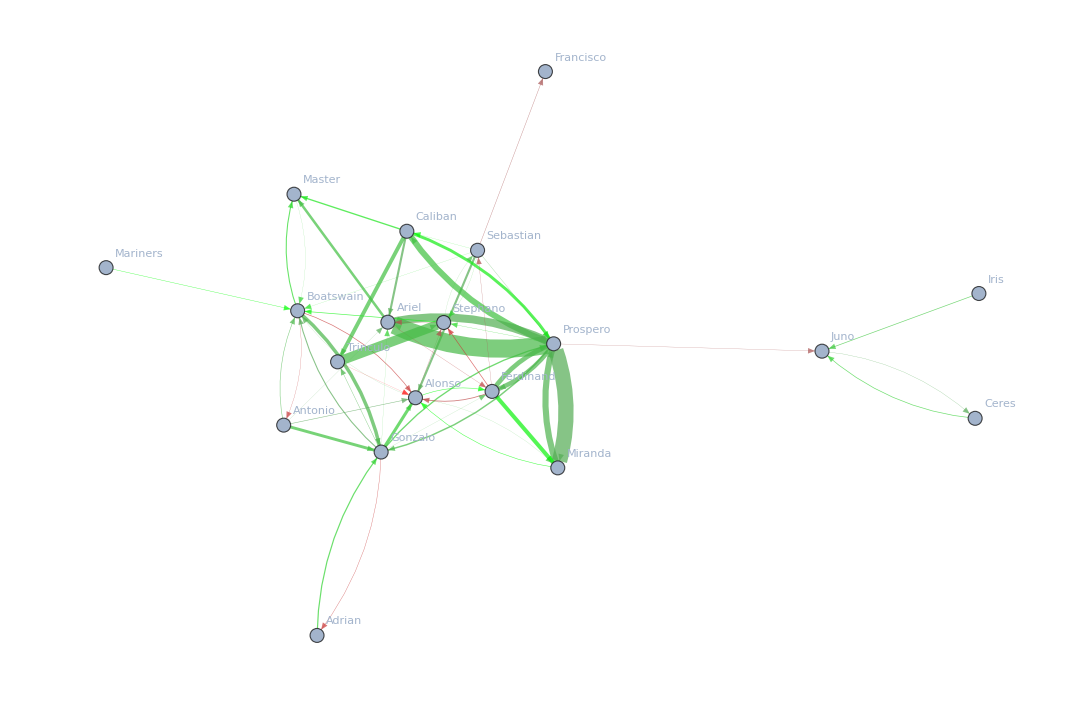

-Graphics-

```mathematica
edgeThickness=Thread[viableRules->(Thickness[#]&/@viableThickness)];
edgeFormat=Table[viableRules⟦i⟧->Directive[Values[edgeThickness]⟦i⟧,Values[edgeColors]⟦i⟧],{i,1,Length[edgeColors]}];
g=Graph[nameList,viableRules,VertexLabels->All,EdgeStyle->edgeFormat]
cgp=CommunityGraphPlot[g]
```